```mathematica
ThisIsAFunction[x_,n_]:=Sin[ Log[n x]]

xs = Table[10^-n,{n,-5,1,0.05}];
data = Table[Table[{x,ThisIsAFunction[x,n]}, {x,xs}],{n,1,5}];

Export["data1.csv", data[[1]]];
Export["data2.csv", data[[2]]];
Export["data3.csv", data[[3]]];
Export["data4.csv", data[[4]]];
Export["data5.csv", data[[5]]];
```

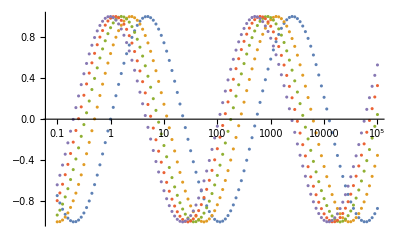

```mathematica
ListLogLinearPlot[data]
```